```mathematica
(* Provide input file path *)

file="Conserved Regions.fasta";

Header=Import[file,"Header"];
Length[Header]
Seq=Import[file,"Sequence"];
Length[Seq]
```

101

101

```mathematica
(* Analysis loop *)

AnalyseListe={};


(* Load hydro-scale *)
HydroReihenfolge={"W","F","I","L","C","M","V","Y","P","A","T","H","G","S","Q","N","E","D","K","R"};
HydroValue={1.,0.859,0.862,0.8310000000000001,0.782,0.687,0.684,0.604,0.46,0.405,0.39,0.35000000000000003,0.31,0.298,0.242,0.132,0.113,0.012,0.006,0.};
(* Re-scaled values of Table 2 from Pliska and Fauchere, 1983 *)


Monitor[

Do[{holen=Seq[[a]],
NamenHolen=Header[[a]],

DomLength=N[StringLength[holen]],

(* All percentages are normalized according to the full length sequences without GLEBS domain *)

NGly=N[StringCount[holen, "G"]/StringLength[holen]]*100;
NAla=N[StringCount[holen, "A"]/StringLength[holen]]*100;
NVal=N[StringCount[holen, "V"]/StringLength[holen]]*100;
NLeu=N[StringCount[holen, "L"]/StringLength[holen]]*100;
NIle=N[StringCount[holen, "I"]/StringLength[holen]]*100;
NPhe=N[StringCount[holen, "F"]/StringLength[holen]]*100;
NTyr=N[StringCount[holen, "Y"]/StringLength[holen]]*100;
NTrp=N[StringCount[holen, "W"]/StringLength[holen]]*100;
NMet=N[StringCount[holen, "M"]/StringLength[holen]]*100;
NCys=N[StringCount[holen, "C"]/StringLength[holen]]*100;
NSer=N[StringCount[holen, "S"]/StringLength[holen]]*100;
NThr=N[StringCount[holen, "T"]/StringLength[holen]]*100;
NAsn=N[StringCount[holen, "N"]/StringLength[holen]]*100;
NGln=N[StringCount[holen, "Q"]/StringLength[holen]]*100;
NAsp=N[StringCount[holen, "D"]/StringLength[holen]]*100;
NGlu=N[StringCount[holen, "E"]/StringLength[holen]]*100;
NLys=N[StringCount[holen, "K"]/StringLength[holen]]*100;
NR=N[StringCount[holen, "R"]/StringLength[holen]]*100;
NPro=N[StringCount[holen, "P"]/StringLength[holen]]*100;
NHis=N[StringCount[holen, "H"]/StringLength[holen]]*100;


NNQ=NAsn+NGln;
NTS=NThr+NSer;
NDE=NAsp+NGlu;
NRK=NR+NLys;
NDERK=NDE+NRK;
NFILVM=NPhe+NIle+NLeu+NVal+NMet;
NFILVMP=NPhe+NIle+NLeu+NVal+NMet+NPro;

FILVM=AppendTo[FILVM,NFILVM];
FILVMP=AppendTo[FILVMP,NFILVMP];

AbsCharge=((N[StringCount[holen, "R"]]+N[StringCount[holen, "K"]])-(N[StringCount[holen, "D"]]+N[StringCount[holen, "E"]]));
Ladung=(((N[StringCount[holen, "R"]]+N[StringCount[holen, "K"]])+(N[StringCount[holen, "D"]]+N[StringCount[holen, "E"]]))/DomLength);

HydroContributions={};
Do[{HydroContributions=AppendTo[HydroContributions,HydroValue[[x]]*StringCount[holen,HydroReihenfolge[[x]]]]},{x,1,Length[HydroReihenfolge]}],
Hydrophobicity=Total[HydroContributions],

RelativeHydrophobicity=Hydrophobicity/DomLength,

ID=StringJoin["AnalyseMarke_",ToString[a]],


AnalyseEinzelErgebnisse={ID,NamenHolen,
DomLength,
Hydrophobicity,RelativeHydrophobicity,NFILVM,NFILVMP,
AbsCharge,Ladung,NDE,NRK,NDERK,
NGly,NAla,NVal,NLeu,NIle,NPhe,NTyr,NTrp,NMet,NCys,NSer,NThr,NAsn,NGln,NAsp,NGlu,NLys,NR,NPro,NHis,
NNQ,NTS};

AnalyseListe=AppendTo[AnalyseListe,AnalyseEinzelErgebnisse]


},{a,1,Length[Seq]}],ProgressIndicator[a,{1,Length[Sequenzen]}]];

Print["\n",Style["Done!",Bold,Blue],"\n"]
```

Done!

OK

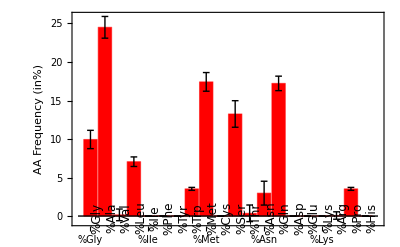

Lfd.-Nr. | Parameter | Mean | StDev | Median | MedianDeviation | Min | Max
3 | Domain length | 28.4158 | 1.32112 | 29. | 0. | 21. | 29.
4 | Hydrophobicity | 12.7002 | 0.374293 | 12.856 | 0. | 10.687 | 13.12
5 | Hydrophobicity/100aa | 0.447395 | 0.0109547 | 0.44331 | 0. | 0.419621 | 0.508905
6 | %FILVM | 24.6276 | 1.53841 | 24.1379 | 0. | 20.6897 | 33.3333
7 | %FILVMP | 28.1556 | 1.71304 | 27.5862 | 0. | 24.1379 | 38.0952
8 | Absolute Charge | 0.019802 | 0.140014 | 0. | 0. | 0. | 1.
9 | Charge/100aa | 0.000682827 | 0.00482807 | 0. | 0. | 0. | 0.0344828
10 | %DE | 0. | 0. | 0. | 0. | 0. | 0.
11 | %RK | 0.0682827 | 0.482807 | 0. | 0. | 0. | 3.44828
12 | %DERK | 0.0682827 | 0.482807 | 0. | 0. | 0. | 3.44828
13 | %Gly | 9.94042 | 1.18871 | 10.3448 | 0. | 7.14286 | 13.7931
14 | %Ala | 24.5043 | 1.40981 | 24.1379 | 0. | 17.2414 | 28.5714
15 | %Val | 0.152953 | 0.75847 | 0. | 0. | 0. | 4.
16 | %Leu | 7.05597 | 0.621521 | 6.89655 | 0. | 3.44828 | 10.3448
17 | %Ile | 0. | 0. | 0. | 0. | 0. | 0.
18 | %Phe | 0. | 0. | 0. | 0. | 0. | 0.
19 | %Tyr | 0. | 0. | 0. | 0. | 0. | 0.
20 | %Trp | 3.52798 | 0.192663 | 3.44828 | 0. | 3.44828 | 4.7619
21 | %Met | 17.4187 | 1.21207 | 17.2414 | 0. | 10.3448 | 23.8095
22 | %Cys | 0. | 0. | 0. | 0. | 0. | 0.
23 | %Ser | 13.2527 | 1.72451 | 13.7931 | 0. | 7.40741 | 17.2414
24 | %Thr | 0.355108 | 1.07698 | 0. | 0. | 0. | 3.84615
25 | %Asn | 2.97288 | 1.54698 | 3.44828 | 0. | 0. | 7.40741
26 | %Gln | 17.2228 | 0.939689 | 17.2414 | 0. | 9.52381 | 18.5185
27 | %Asp | 0. | 0. | 0. | 0. | 0. | 0.
28 | %Glu | 0. | 0. | 0. | 0. | 0. | 0.
29 | %Lys | 0. | 0. | 0. | 0. | 0. | 0.
30 | %Arg | 0.0682827 | 0.482807 | 0. | 0. | 0. | 3.44828
31 | %Pro | 3.52798 | 0.192663 | 3.44828 | 0. | 3.44828 | 4.7619
32 | %His | 0. | 0. | 0. | 0. | 0. | 0.
33 | %NQ | 20.1956 | 1.88647 | 20.6897 | 0. | 9.52381 | 25.9259
34 | %TS | 13.6078 | 2.09151 | 13.7931 | 0. | 7.40741 | 17.8571

```mathematica
(* Analyzing the parameter distributions *)

TransposedList=Transpose[AnalyseListe];

TableData={};
ChartData={};

Numerierung=Table[i,{i,Length[labels]}];

labels={"ID","Name",
"Domain length",
"Hydrophobicity","Hydrophobicity/100aa","%FILVM","%FILVMP",
"Absolute Charge","Charge/100aa","%DE","%RK","%DERK",
"%Gly","%Ala","%Val","%Leu","%Ile","%Phe","%Tyr","%Trp","%Met","%Cys","%Ser","%Thr","%Asn","%Gln","%Asp","%Glu","%Lys","%Arg","%Pro","%His",
"%NQ","%TS"};

If[Length[labels]==Length[AnalyseEinzelErgebnisse],Print["OK"],Print[Style["ERROR!",Bold,Red]]]

Do[{mean=Mean[Part[TransposedList,n]],
StDev=StandardDeviation[Part[TransposedList,n]],
median=Median[Part[TransposedList,n]],
MedDev=MedianDeviation[Part[TransposedList,n]],
min=Min[Part[TransposedList,n]],
max=Max[Part[TransposedList,n]],
(* Histo=Histogram[TransposedList[[n]],PlotLabel->Part[labels,n-2]],Print[Histo], *)
TableData=AppendTo[TableData,{Numerierung[[n]],labels[[n]],N[mean],N[StDev],N[median],N[MedDev],N[min],N[max]}],
ChartData=AppendTo[ChartData,{mean->StDev}]},
{n,3,Length[TransposedList]}]

ChartData=Flatten[ChartData];

errorBar[type_:"Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error},error=Flatten[meta];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},value,meta],{Black,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}]

Bar=BarChart[ChartData[[11;;30]],ChartElementFunction->errorBar["Rectangle"],ChartLabels->Placed[labels[[13;;32]],Axis,Rotate[Style[#,12,FontFamily->"Arial"],Pi/2]&],Frame->Left,FrameLabel->{None,Style["AA Frequency (in%)",12,FontFamily->"Arial"]},
ChartStyle->Red]


TableHead={Style["Lfd.-Nr.",Bold],Style["Parameter",Bold],Style["Mean",Bold],Style["StDev",Bold],Style["Median",Bold],Style["MedianDeviation",Bold],Style["Min",Bold],Style["Max",Bold]};
tabelle=TableForm[PrependTo[TableData,TableHead]]
```

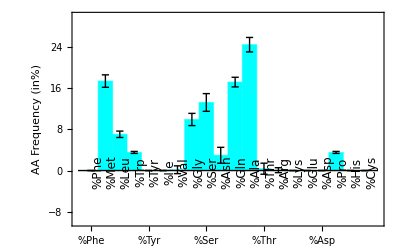

```mathematica
(* Manually re-order chart data for nice plot *)

NewChartData={
ChartData[[16]],
ChartData[[19]],
ChartData[[14]],
ChartData[[18]],
ChartData[[17]],
ChartData[[15]],
ChartData[[13]],
ChartData[[11]],
ChartData[[21]],
ChartData[[23]],
ChartData[[24]],
ChartData[[12]],
ChartData[[22]],
ChartData[[28]],
ChartData[[27]],
ChartData[[26]],
ChartData[[25]],
ChartData[[29]],
ChartData[[30]],
ChartData[[20]]};

NewLabels={
"%Phe",
"%Met",
"%Leu",
"%Trp",
"%Tyr",
"%Ile",
"%Val",
"%Gly",
"%Ser",
"%Asn",
"%Gln",
"%Ala",
"%Thr",
"%Arg",
"%Lys",
"%Glu",
"%Asp",
"%Pro",
"%His",
"%Cys"
};


BarNeu=BarChart[NewChartData,
ChartElementFunction->errorBar["Rectangle"],ChartLabels->Placed[NewLabels,Axis,Rotate[Style[#,12,FontFamily->"Arial"],Pi/2]&],
Frame->Left,FrameLabel->{None,Style["AA Frequency (in%)",12,FontFamily->"Arial"]},
ChartStyle->Cyan,
BarSpacing->None,
PlotRange->{Automatic,{-10,30}}]
```

```mathematica
(* Export the data *)

dir=DirectoryName[file];
SetDirectory[dir];
newdir=CreateDirectory["CR analysis"];
SetDirectory[newdir];

Export["Statistics summary.pdf",tabelle]
Export["CR bar.pdf",BarNeu]
```

Statistics summary.pdf

CR bar.pdf